# Time Tagger Quickstart

## Initialization

## Establish .NET connection

```mathematica
Needs["NETLink`"];
(* loads NETLink package to create a .NET context *)
InstallNET[];
(* launches the .NET runtime and prepares it to be used from Mathematica *)
TimeTagger = LoadNETAssembly["SwabianInstruments.TimeTagger"];
(* loads the SwabianInstruments.TimeTagger assembly into the .NET runtime *) 
(* returns to TimeTagger the expression that can be used to identify the assembly *)
TT = NETNew["SwabianInstruments.TimeTagger.TT"];
(* constructs a new .NET object TT of type "SwabianInstruments.TimeTagger.TT" *)
```

## Create a Time Tagger instance

```mathematica
tagger = TT@createTimeTagger[];
(* create Time Tagger instance with the name tagger *)
(* alternative synthex: TT[createTimeTagger[]] *)
```

## Utilities

```mathematica
SetDirectory[NotebookDirectory[]];
(* Sets a directory for data export - current folder with Mathematica notebook *)

(*** Small convinient functions converting time to ps ***)
ps[t_]:=t;
ns[t_]:=t*10^3;
us[t_]:=t*10^6;
ms[t_]:=t*10^9;
s[t_]:=t*10^12;
(* Example: ms[1] or 1//ms equals to 1*1E9 *)
```

## Measurements using physical channels

## Demonstrate a counter time trace

Create counters on channels 1 and 2 with 1
 ms bin width and 1000 points.

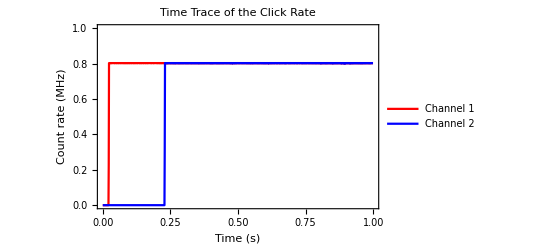

```mathematica
count =NETNew["SwabianInstruments.TimeTagger.Counter", tagger, {1,2},1//ms, 1000];
(* construct a new measurement "count" of class Counter *)
count@startFor[1//s]
(* run the "count" for exactly 1 s *)
Pause[0.1]
tagger@setTestSignal[1,True];
(* pause and set a test signal for the first channel *)
Pause[0.2]
tagger@setTestSignal[2,True];
(* pause and set a test signal for the second channel *)
While[count@isRunning[],Pause[0.1]]
(* wait until the "count" measurement is done *)
tagger@setTestSignal[{1,2},False];
(* disable the test signals at the channels 1 and 2 *)

x =N[ count@getIndex[]* 10^-12];
(* take an array of time indexes in ps from the result of "count", convert to seconds, save to x *)
y=N[count@getData[]/10^-3*10^-6];
(* take arrays of data in [clicks per bin] for two channels from the result of "count" *)
(* convert [clicks per bin] to click rate in Hz, dividing by the binwidth of 1 ms *)
(* then convert the click rate to MHz, multiplying by 10^-6 *)
ClickRate=Table[{x⟦i⟧,y⟦ch⟧⟦i⟧},{ch,{1,2}},{i,1,Length[x]}];
(* data for click rate on channels 1 and 2 in table form *)
ListLinePlot[ClickRate,Frame->True, PlotStyle->{{Thick,Red},{Thick,Blue}},PlotRange-> {{0,1},{0,1}}, FrameLabel-> {"Time (s)", "Count rate (MHz)"}, PlotLabel->"Time Trace of the Click Rate", PlotLegends-> {"Channel 1","Channel 2"}]
(* plots the click rate trace *)

(*** Data export into a .txt file to the folder with the Mathematica notebook ***)
(* Every time export rewrites the existing .txt file *)
Export["ClickRate.txt",Table[{x⟦i⟧,y⟦1⟧⟦i⟧,y⟦2⟧⟦i⟧},{i,1,Length[x]}],"Table"];
```

## Determination of the internal propagation delay

Create a cross-correlation on channels 1 and 2 with 10 ps bin width and 400 points.

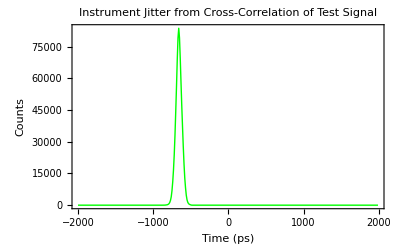

The internal propagation delay is -660 ps.

```mathematica
tagger@setTestSignal[{1,2},True];
(* set a test signals at the channels 1 and 2 *)
corr = NETNew["SwabianInstruments.TimeTagger.Correlation", tagger, 1, 2,10//ps,400 ];
(* construct a new measurement "corr" of class Correlation *)
corr@startFor[1//s];
While[corr@isRunning[],Pause[0.1]]
(* run "corr" for exactly 1 second *)
tagger@setTestSignal[{1,2},False];
(* disable the test signals at the channels 1 and 2 *)
xcorr= corr@getIndex[];
(* array of time indexes in ps from the "corr" measurement *)
ycorr  = corr@getData[];
(* array of y-values from "corr" measurement *)
corrData=Table[{xcorr⟦i⟧,ycorr⟦i⟧},{i,1,Length[xcorr]}];
(* create table of {x,y} values for plotting and export *)
ListLinePlot[corrData,Frame->True,PlotRange-> Full, PlotStyle->{{Thick,Green}}, FrameLabel-> {"Time (ps)", "Counts"}, PlotLabel->"Instrument Jitter from Cross-Correlation of Test Signal"]
(* plot the cross-correlation function *)

delay =xcorr⟦FirstPosition[ycorr,Max[ycorr]]⟦1⟧⟧;
(* calculate the internal propagation delay *)
StringForm["The internal propagation delay is `` ps.", delay]
(* print the internal propatation delay *)

(*** Data export into a .txt file to the folder with the Mathematica notebook ***)
(* Every time export rewrites the existing .txt file *)
Export["CrossCorrelation.txt",corrData,"Table"];
```

## Measurements using virtual channels

## Combined vs. coinciding counts

Create virtual channels that either combine the events in channel 1 and channel 2 or collect coinciding events, respectively.

```mathematica
tagger@setTestSignal[{1,2},True];
(* set a test signals at the channels 1 and 2 *)
Ch1orCh2 = NETNew["SwabianInstruments.TimeTagger.Combiner", tagger, {1,2}];
(* create a virtual channel that combines events from physical channels 1 and 2 *)
CombCh=Ch1orCh2@getChannel[];
Print["The virtual channel combining channels 1 & 2 has been assigned a number ", CombCh];
(* print the number automatically assigned for virtual combiner *)
Ch1andCh2 = NETNew["SwabianInstruments.TimeTagger.Coincidence", tagger, {1,2}, Abs[delay], 0];
(* create a virtual channel for coinciding events at physical channels 1 and 2 *)
(* take the internal propagation delay as coinicidence window *)
(* time-stamp the coincidence by the last event completing  coincidence *)
(* types of time stamp for coincidence: 0 - Last,  1 - Average, 2 - First, 3 - Listed First *)
CoincCh= Ch1andCh2@getChannel[];
Print["The virtual channel for coinciding clicks has been assigned a number ",CoincCh];
(* print the number automatically assigned for virtual coincidence channel *)
countrate = NETNew["SwabianInstruments.TimeTagger.Countrate", tagger, {1,2,CombCh, CoincCh}];
(* "countrate" measures the average countrates in [counts per second] *) (* for the physical channels with test signal and for the virtual channels with combined and coinciding events *)
countrate@startFor[1//s];
While[countrate@isRunning[],Pause[0.1]]
(* run "countrate" for exactly 1 second *)
tagger@setTestSignal[{1,2},False];
(* disable the test signals at the channels 1 and 2 *)
data = countrate@getData[];
(* get data and print the results *)
Print["Count rate at Channel 1: ", ScientificForm[data⟦1⟧]];
Print["Count rate at Channel 2: ", ScientificForm[data⟦2⟧]];
Print["Count rate at combined channel: ", ScientificForm[data⟦3⟧]];
Print["Count rate at coincidence channel: ", ScientificForm[data⟦4⟧]];
```

The virtual channel combining channels 1 & 2 has been assigned a number 1028

The virtual channel for coinciding clicks has been assigned a number 1029

Count rate at Channel 1: 8.02589×10^5

Count rate at Channel 2: 8.02589×10^5

Count rate at combined channel: 1.60518×10^6

Count rate at coincidence channel: 4.50892×10^5

## Finish

```mathematica
TT@freeTimeTagger[tagger];
(* release the Time Tagger *)
```